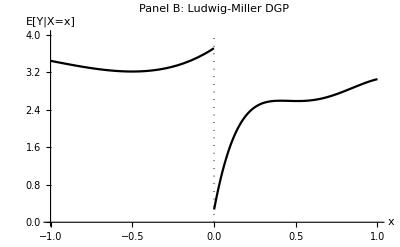

```mathematica
tauY=0.26-3.71;
beta0Yr=0.26;
beta0Yl=3.71;
beta1Yr=18.49;
beta1Yl=2.30;
beta2Yr=-54.81;
beta2Yl=3.28;
beta3Yr=74.30;
beta3Yl=1.45;
beta4Yr=-45.02;
beta4Yl=0.23;
beta5Yr=9.83;
beta5Yl=0.03;

fl[x_]:=beta0Yl+beta1Yl x+beta2Yl x^2+beta3Yl x^3+beta4Yl x^4+beta5Yl x^5;
fr[x_]:=beta0Yr+beta1Yr x+beta2Yr x^2+beta3Yr x^3+beta4Yr x^4+beta5Yr x^5;

vertical=Line[{{0,0},{0,4}}];
DGPLM=Plot[Piecewise[{{fl[x],x<0},{fr[x],x>0}}],{x,-1,1},
	PlotStyle-> {Black},
	PlotLabel-> "Panel B: Ludwig-Miller DGP",
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[Y|X=x]"},
	AxesOrigin->{-1,0},
	PlotRange->{{-1,1},{0,4}},
	Epilog->{Directive[Dotted],vertical}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RD DGP LM.pdf",DGPLM, ImageSize->Medium];
```